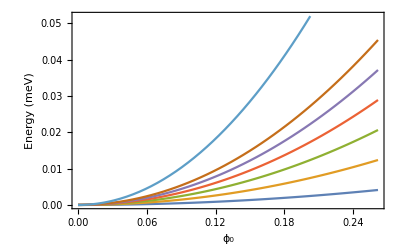

```mathematica
ℏ = 6.582*10^(-16); (*6.52*10^-16 [eV*s]*)
c = 2.998*10^8 ;(*2.998*10^8 [m/s]*)
q = 1.602*10^(-19);(*[C]*)
Subscript[m, e] = 0.51*10^6/c^2; (*0.51 [MeV/c^2]*)

hw = 191*10^(-3);(*191 [mEv]*)
Emax = 5*10^7; (*[V/m]*)
d = 100*10^(-9);(*[m]*)
K = 2*π/d; (*[m^-1]*)

m = 1*Subscript[m, e];
a = 1*10^(-9);(*[m]*)

phimax = Emax*a/hw;(*unitless*)
w[n_]:= 10^3*((n+0.5)(ℏ^2 * K / (m*a))^2 * x^2 / hw - (K^2*ℏ^6/(16*m^3*a^4))*x^4/hw^2);
Plot[{w[0],w[1],w[2],w[3],w[4],w[5], w[10]}, {x,0,phimax}, Frame->True,FrameLabel->{"ϕ_0", "Energy (meV)","",""}]
```